## Madgraph

```mathematica
(*THIS NOTEBOOK RUNS A SINGLE SET OF PARAMETERS THROUGH PYTHIA + (optionally) BOOST FOR INSPECTION OF THE SPECTRUM*)
If[$Notebooks==True,SetDirectory[NotebookDirectory[]],SetDirectory[Directory[]]];

nevents=10000;
minDP=0.001;
maxDP=10.^1;
pointsDP=100;
DPmasstab=Table[10.^lmA,{lmA,Log10[minDP],Log10[maxDP],(Log10[maxDP]-Log10[minDP])/(pointsDP-1)}]
(*DPmasstab={0.05}*)
minϵ=10.^-10;
maxϵ=10^-2;
pointsϵ=100;
ϵtab=Table[10.^lϵ,{lϵ,Log10[minϵ],Log10[maxϵ],(Log10[maxϵ]-Log10[minϵ])/(pointsϵ-1)}]
DMmass=200000.;
(*These are parameters to be used in the MG5 scan -- they mostly don't matter for the model independent case*)
MGϵ=1. 10^-5;(*Mixing parameter between photon and dark photon -- doesn't really matter for the model independent scan here*)
MGαχ=0.024/1000. DMmass;(*Dark fine structure constant -- also doesn't matter here*)
MGmχ=DMmass;(*DM mass -- only need it big enough to avoid the DP decaying into them*)

hawcbins={{0.5,1.6,2.2 10^-12},{1.6,5.0,8.8 10^-13},{5.0,15.7,2.8 10^-13},{15.7,50,8.1 10^-14},{50,158,6.3 10^-14}};(*Start of bin (left edge) and flux limit in TeV and TeV cm^2 s^-1 respectively*)

(*fixedform is what makes the numbers nice to print to a file*)
StringPadLeft["",1];(*this must be evaluated first for no evident reason*)fixedform[numd_,data_]:=Module[{ef},ef[s_String/;StringTake[s,1]=="-"]:="-"<>StringPadLeft[StringTake[s,{2,-1}],2,"0"];
ef[s_String]:="+"<>StringPadLeft[s,2,"0"];
NumberForm[data,{numd,numd},ExponentFunction->(#&),NumberSigns->{"-"," "},NumberFormat:>(Row[{StringPadRight[#1,numd+2,"0"],"E",ef[#3]}]&)]]
$mg5outputfile = "DPdvb";
$widthsfile="DPwidths";
$widthsfixfile="DPwidthsfix";
$inputfile="DPanninput";
$mg5runfile="DPmg5run";
$pythiaoutputfile="DPpythiaoutput";
$pythonoutputfile="DPpythonoutput";
$perannspecfile="DPperannspec";
$boostspecfile="DPboostspec";
$efluxfile="DPeflux";
$scanfile="DPfullscan";
$debugfile = "debug"<>$mg5outputfile;
talpha="thermal";
If[FileExistsQ[$debugfile],DeleteFile[$debugfile]];
```

{0.001,0.0010975,0.0012045,0.00132194,0.00145083,0.00159228,0.00174753,0.00191791,0.0021049,0.00231013,0.00253536,0.00278256,0.00305386,0.0033516,0.00367838,0.00403702,0.00443062,0.0048626,0.0053367,0.00585702,0.00642807,0.0070548,0.00774264,0.00849753,0.00932603,0.0102353,0.0112332,0.0123285,0.0135305,0.0148497,0.0162975,0.0178865,0.0196304,0.0215443,0.0236449,0.0259502,0.0284804,0.0312572,0.0343047,0.0376494,0.0413201,0.0453488,0.0497702,0.0546228,0.0599484,0.0657933,0.0722081,0.0792483,0.0869749,0.0954548,0.104762,0.114976,0.126186,0.138489,0.151991,0.16681,0.183074,0.200923,0.220513,0.242013,0.265609,0.291505,0.319927,0.351119,0.385353,0.422924,0.464159,0.509414,0.559081,0.613591,0.673415,0.739072,0.811131,0.890215,0.97701,1.07227,1.17681,1.29155,1.41747,1.55568,1.70735,1.87382,2.05651,2.25702,2.47708,2.71859,2.98365,3.27455,3.59381,3.94421,4.32876,4.75081,5.21401,5.72237,6.28029,6.89261,7.56463,8.30218,9.11163,10.}

{1.×10^-10,1.2045×10^-10,1.45083×10^-10,1.74753×10^-10,2.1049×10^-10,2.53536×10^-10,3.05386×10^-10,3.67838×10^-10,4.43062×10^-10,5.3367×10^-10,6.42807×10^-10,7.74264×10^-10,9.32603×10^-10,1.12332×10^-9,1.35305×10^-9,1.62975×10^-9,1.96304×10^-9,2.36449×10^-9,2.84804×10^-9,3.43047×10^-9,4.13201×10^-9,4.97702×10^-9,5.99484×10^-9,7.22081×10^-9,8.69749×10^-9,1.04762×10^-8,1.26186×10^-8,1.51991×10^-8,1.83074×10^-8,2.20513×10^-8,2.65609×10^-8,3.19927×10^-8,3.85353×10^-8,4.64159×10^-8,5.59081×10^-8,6.73415×10^-8,8.11131×10^-8,9.7701×10^-8,1.17681×10^-7,1.41747×10^-7,1.70735×10^-7,2.05651×10^-7,2.47708×10^-7,2.98365×10^-7,3.59381×10^-7,4.32876×10^-7,5.21401×10^-7,6.28029×10^-7,7.56463×10^-7,9.11163×10^-7,1.0975×10^-6,1.32194×10^-6,1.59228×10^-6,1.91791×10^-6,2.31013×10^-6,2.78256×10^-6,3.3516×10^-6,4.03702×10^-6,4.8626×10^-6,5.85702×10^-6,7.0548×10^-6,8.49753×10^-6,0.0000102353,0.0000123285,0.0000148497,0.0000178865,0.0000215443,0.0000259502,0.0000312572,0.0000376494,0.0000453488,0.0000546228,0.0000657933,0.0000792483,0.0000954548,0.000114976,0.000138489,0.00016681,0.000200923,0.000242013,0.000291505,0.000351119,0.000422924,0.000509414,0.000613591,0.000739072,0.000890215,0.00107227,0.00129155,0.00155568,0.00187382,0.00225702,0.00271859,0.00327455,0.00394421,0.00475081,0.00572237,0.00689261,0.00830218,0.01}

```mathematica
If[FileExistsQ["pythia8_card_"<>$mg5outputfile<>".dat"],DeleteFile["pythia8_card_"<>$mg5outputfile<>".dat"]];
CopyFile["pythia8_card_default.dat","pythia8_card_"<>$mg5outputfile<>".dat"];
pythiacard=OpenAppend["pythia8_card_"<>$mg5outputfile<>".dat",PageWidth-> 500];
WriteString[pythiacard,"ResonanceWidths:minWidth = 1e-30"];
(*WriteString[pythiacard,"\n"<>"50:all = dvb dvb 1 0 0 0.1 0.0011"];*)
(*This enables particles with very small widths to still decay by avoiding their width being set to zero for being below the default min of 1e-20*)
WriteString[pythiacard,"\n"<>"Check:event = off"];
WriteString[pythiacard,"\n"<>"211:mayDecay = true"];(*π^(+-)*)
WriteString[pythiacard,"\n"<>"13:mayDecay = true"];(*muons*)
WriteString[pythiacard,"\n"<>"321:mayDecay = true"];(*K^+*)
WriteString[pythiacard,"\n"<>"130:mayDecay = true"];(*Subscript[K, L]^0*)
(*WriteString[pythiacard,"\n"<>"Beams:eCM = "<>ToString[2.00002 DPmass]];*)
(*WriteString[pythiacard,"\n"<>"50:isResonance = false"];*)
(*WriteString[pythiacard,"\n"<>"Check:epTolErr = 1000."];*)
(*WriteString[pythiacard,"\n"<>"50:onMode = on"];*)
(*WriteString[pythiacard,"\n"<>"100001:offIfMatch = 1 1"];*)
(*WriteString[pythiacard,"\n"<>"SigmaTotal:setOwn = on"];*)
(*WriteString[pythiacard,"\n"<>"SigmaTotal:sigmaTot = 80"];*)

(*WriteString[pythiacard,"\n"<>"100001:oneChannel = onMode 1. 0. 11 -11"];*)

(*WriteString[pythiacard,"\n"<>"ParticleDecays:allowPhotonRadiation = on"];*)
(*WriteString[pythiacard,"\n"<>"ParticleDecays:limitTau0 = off"];
WriteString[pythiacard,"\n"<>"ParticleDecays:limitTau = off"];
WriteString[pythiacard,"\n"<>"ParticleDecays:limitRadius = off"];
WriteString[pythiacard,"\n"<>"ParticleDecays:limitCylinder = off"];
WriteString[pythiacard,"\n"<>"ParticleDecays:mSafety = 0."];*)
Close[pythiacard];
```

```mathematica
(*This sets up the scan to annihilate electron/positron into dark photons AT REST*)
ScanMadgraph[DPmasstable_,calcw_]:=(
If[FileExistsQ[$mg5runfile],DeleteFile[$mg5runfile]];
If[$Notebooks==False,If[DirectoryQ[$mg5outputfile],DeleteDirectory[$mg5outputfile,DeleteContents->True]]];
mg5run={"import model ./SMDP_UFO/",
 "set automatic_html_opening False",
 (*"generate e+ e- > dvb dvb",*)
"generate ~xd ~xd~ > dvb dvb",
"output " <> $mg5outputfile,
"launch "<>$mg5outputfile,
"shower = Pythia8",
"set nevents "<>ToString[nevents],
"set ptj 0.0",
"set pta 0.0",
"set ptl 0.0",
(*"set drll 0.0",
"set drjj 0.0",
"set draj 0.0",
"set drjl 0.0",
"set dral 0.0",
"set draa 0.0",
"set r0gamma 0.01",*)
"set etaj -1.0",
"set etaa -1.0",
"set etal -1.0",
"./pythia8_card_"<>$mg5outputfile<>".dat\n"};
Export[$mg5runfile,mg5run,"text"];

runfile=OpenAppend[$mg5runfile,PageWidth-> 500];
Do[
If[calcw≠ 1,WriteString[runfile,"./DPparam_card_AutoWidth_default.dat\n"];];
WriteString[runfile,"set gsm "<> ToString[fixedform[6,MGϵ]]<>"\n"];
WriteString[runfile,"set adm "<> ToString[fixedform[6,MGαχ]]<>"\n"];
WriteString[runfile,"set mdvb "<> ToString[fixedform[6,DPmasstable⟦i⟧]]<>"\n"];
WriteString[runfile,"set mxd "<> ToString[fixedform[6,MGmχ]]<>"\n"];
WriteString[runfile,"set ebeam1 "<> ToString[fixedform[6,DMmass*1.00001]]<>"\n"];
WriteString[runfile,"set ebeam2 "<> ToString[fixedform[6,DMmass*1.00001]]<>"\n"];
If[calcw==1,WriteString[runfile,"set WDVB Auto\n"];];
If[i≠Length[DPmasstable],WriteString[runfile,"launch "<>(*$mg5outputfile<>*)"\n"]];
,{i,Length[DPmasstable]}];
Close[runfile];

If[$Notebooks==False,Run["mg5_aMC "<>$mg5runfile]];)
```

```mathematica
pythiaread[]:=
(fn=FileNames[All,$mg5outputfile<>"/Events"];
pn=FileNames[$pythiaoutputfile<>"*"];
Do[
If[FileExistsQ[pn⟦i⟧],DeleteFile[pn⟦i⟧]];
,{i,1,Length[pn]}];
Do[
Run["gzip -d < "<>fn⟦i⟧<>"/tag_1_pythia8_events.hepmc.gz > ./"<>$pythiaoutputfile<>StringTake[fn⟦i⟧,-2]];
,{i,1,Length[fn]}];
pn=FileNames[$pythonoutputfile<>"*"];
Do[
If[FileExistsQ[pn⟦i⟧],DeleteFile[pn⟦i⟧]];
,{i,1,Length[pn]}];
Do[
Run["python readspec.py "<>$pythiaoutputfile<>StringTake[fn⟦i⟧,-2]<>" "<>$pythonoutputfile<>StringTake[fn⟦i⟧,-2]];
,{i,1,Length[fn]}];)
```

```mathematica
readwidth[path_,PDG_]:=(fno=OpenRead[path];
SetStreamPosition[fno,0];
fnf=Find[fno,"DECAY "<>" "<>PDG];
str=StringTake[fnf,{StringPosition[fnf,PDG][[1,2]]+4,StringPosition[fnf,PDG][[1,2]]+15}];
width=ToExpression[StringReplace[str,{"e+"-> "*10^","e-"-> "*10^-"}]];
Close[fno];
width
)
readwidths[PDG_]:=(
fn=FileNames[All,$mg5outputfile<>"/Events"];
fnb=fn;
widths={};
Do[
fnb⟦fni⟧=fn⟦fni⟧<>"/"<>StringTake[fn⟦fni⟧,{StringPosition[fn⟦fni⟧,"run_"][[1,1]],StringLength[fn⟦fni⟧]}]<>"_tag_1_banner.txt";
widths =Append[widths,readwidth[fnb⟦fni⟧,PDG]],{fni,1,Length[fn]}];
widths
)
```

## Solar Data

```mathematica
build=0;
If[$Notebooks==True,SetDirectory[NotebookDirectory[]],SetDirectory[Directory[]]];
SSM=Import["data/agss09.dat"];
aucm=1.495 10^13(*Distance to earth from sun, in cm*);
aum=1.49598 10^11 ;(*distance from earth to sun in m*)
k=2.5; (*See 1602.01465 Eq. 15/16 for what these constants are*)
u0 = 245 10^3; 
uS=233 10^3;
vgal = 550 10^3;(*Galactic escape velocity in m/s*)
SR=6.9598 10^8;(*Solar radius in m*)
ρχ=0.3 10^6(*Local dark matter density; PDG says 0.3 GeV/c^2 per cm^-3 = 10^6*0.3 GeV/c^2 per m^-3 *);
Gconst=6.67408 10^-11;
mp=0.938272(*proton mass, GeV*);
SM=1.989 10^30(*Solar mass in kg*);
(*Htnf is the total fraction by number of hydrogen in the sun*)
Htnf=0.912;
(*Htmf is the total fraction by mass of hydrogen in the sun*)
Htmf=0.710;
(*Total number of atoms in the sun*)
tn=(Htmf*SM)/(1.007825 au Htnf)/.{au->1.660539 10^-27(*kg*)};

(*THIS IS ELEMENTS USED IN FENG*)
atomscut={"He4","N14","O16","Ne","Mg","Si","S","Fe"};

atomscut={"H1","He4","N14","O16","Ne","Mg","Si","S","Fe"};


Fiinf={{"He4",0.986},{"N14",0.613},{"O16",0.613},{"Mg",0.281},{"Si",0.281},{"Fe",0.00677}};
mic={{"He4",18.2},{"N14",75.2},{"O16",75.2},{"Mg",71.7},{"Si",71.7},{"Fe",29.3}};
αi={{"He4",1.58},{"N14",2.69},{"O16",2.69},{"Mg",2.97},{"Si",2.97},{"Fe",3.36}};
(*FULL LIST OF ELEMENTS*)
atomscut={"H1","He4","He3","C12","C13","N14","N15","O16","O17","O18","Ne","Na","Mg","Al","Si","P","S","Cl","Ar","K","Ca","Sc","Ti","V","Cr","Mn","Fe","Co","Ni"};

(*My list of elements*)
atomscut={"H1","He4","C12","N14","O16","Ne","Na","Mg","Al","Si","P","S","Cl","Ar","K","Ca","Sc","Ti","V","Cr","Mn","Fe","Co","Ni"};


(*Full list of elements: {Name, atomic weight in a.u., number of protons}*)
mNuF={{"H1",1.007825,1},{"He4",4.002603,2},{"He3",3.0160293,2},{"C12",12.,6},{"C13",13.00335483521,6},{"N14",14.00307400446,7},{"N15",15.0001088989,7},{"O16",15.99491461960,8},{"O17",16.9991317566,8},{"O18",17.9991596128,8},{"Ne",20.1797,10},{"Na",22.98976928,11},{"Mg",24.305,12},{"Al",26.9815385,13},{"Si",28.085,14},{"P",30.973761998,15},{"S",32.06,16},{"Cl",35.45,17},{"Ar",39.948,18},{"K",39.0983,19},{"Ca",40.078,20},{"Sc",44.955908,21},{"Ti",47.867,22},{"V",50.9415,23},{"Cr",51.9961,24},{"Mn",54.938043,25},{"Fe",55.845,26},{"Co",58.933194,27},{"Ni",58.6934,28}};
(*element mass functions: {Name, mass [r (m)] (kg) *)
elemfF={};
Do[
elemfF=Append[elemfF,Interpolation[Table[{SSM⟦i,2⟧*SR,SSM⟦i,j⟧},{i,2,Length[SSM]}]]],{j,7,Length[SSM⟦1⟧]}];
(*ndfF is number density function {Name, density [r (m)] (m^-3)}*)
ndfF={};
Do[
ndfF=Append[ndfF,{SSM⟦1,j⟧,Interpolation[Table[{SSM⟦i,2⟧*SR,(SSM⟦i,j⟧(*mass fraction*)*SSM⟦i,4⟧*0.001*100^3(*density (kg/m^3)*))/(mNuF⟦j-6,2⟧*1.660539 10^-27(*kg/u*))},{i,2,Length[SSM]}]]}],{j,7,Length[SSM⟦1⟧]}];
fiF={};
Do[
fiF=Append[fiF,{SSM⟦1,j⟧,NIntegrate[4π r^2 ndfF⟦j-6,2⟧[r],{r,0,SR},WorkingPrecision-> 7]/tn}],{j,7,Length[SSM⟦1⟧]}];


(*an is atomic number of nuclei = mass in au*)
An={};
Do[If[MemberQ[atomscut,mNuF⟦i,1⟧],An=Append[An,mNuF⟦i,2⟧]],{i,1,Length[mNuF]}];
(*mn is mass of nuclei in GeV*)
mn={};
Do[If[MemberQ[atomscut,mNuF⟦i,1⟧],mn=Append[mn,mNuF⟦i,2⟧*0.9314941(*GeV/au*)]],{i,1,Length[mNuF]}];
(*zn is number of protons in each atom*)
zn={};
Do[If[MemberQ[atomscut,mNuF⟦i,1⟧],zn=Append[zn,mNuF⟦i,3⟧]],{i,1,Length[mNuF]}];
(*ndf is number density function [r (m)], m^-3*)
ndf={};
Do[If[MemberQ[atomscut,ndfF⟦i,1⟧],ndf=Append[ndf,ndfF⟦i,2⟧]],{i,1,Length[mNuF]}];
fi={};
Do[If[MemberQ[atomscut,fiF⟦i,1⟧],fi=Append[fi,fiF⟦i,2⟧]],{i,1,Length[mNuF]}];

(*Table[{atomscut⟦i⟧,Log10[NIntegrate[4π r^2 ndf⟦i⟧[r],{r,0,SR}]/(tn*0.92)]+12},{i,1,Length[ndf]}]*)
```

## Generating Functions

### Generate Escape Velocity

```mathematica
If[build==1,
Mtab=Table[{SSM⟦i,2⟧*SR,SSM⟦i,1⟧*SM},{i,2,Length[SSM]}];
Mi=Interpolation[Mtab,InterpolationOrder->1];
vetab= Table[{r,√(-2(NIntegrate[(Gconst Mi[rp])/rp^2,{rp,SR,r}]-(Gconst Mi[SR])/SR))},{r,SR/100,SR,SR/100}];
vetab=Prepend[vetab,{0.0001,√(-2(NIntegrate[(Gconst Mi[rp])/rp^2,{rp,SR,0.001}]-(Gconst Mi[SR])/SR))}];
Export["data/Escape.csv",vetab,"CSV"];]
```

### Generate fS

```mathematica
If[build==1,
fnonorm[u_]:=(*norm*) (Exp[(vgal^2-u^2)/(k u0^2)]-1)^k HeavisideTheta[vgal-u];
(*normconstant=1/NIntegrate[fnonorm[√(x^2+y^2+z^2)],{x,0,vgal},{y,0,vgal},{z,0,vgal}]*)
normconstant=1/NIntegrate[4π u^2 fnonorm[u],{u,0,vgal}];

f[u_]:=normconstant(Exp[(vgal^2-u^2)/(k u0^2)]-1)^k HeavisideTheta[vgal-u];
usolve=Solve[u^2+uS^2+2u uS c==vgal^2,u][[2]];
upint=u/.usolve/.{c->-1};
Export["data/upint.csv",upint,"CSV"];
fS[u_] := 1/2 NIntegrate[f[√(u^2+uS^2+2u uS c)],{c,-1,1}];
ftab=Table[{u,f[u]},{u,0.,upint,upint/1000}];
Export["data/f.csv",ftab,"CSV"];
fStab=Table[{u,fS[u]},{u,0.,upint,upint/1000}];
Export["data/fS.csv",fStab,"CSV"];]
```

## Capture Rate Function

```mathematica
vetab=Import["data/Escape.csv"]//ToExpression;
vei=Interpolation[vetab,InterpolationOrder->1];
fStab=Import["data/fS.csv"]//ToExpression;
fSi=Interpolation[fStab];
fnonorm[u_]:=(*norm*) (Exp[(vgal^2-u^2)/(k u0^2)]-1)^k HeavisideTheta[vgal-u];
normconstant=1/NIntegrate[4π u^2 fnonorm[u],{u,0,vgal}];

f[u_]:=normconstant(Exp[(vgal^2-u^2)/(k u0^2)]-1)^k HeavisideTheta[vgal-u];
usolve=Solve[u^2+uS^2+2u uS c==vgal^2,u][[2]];
upint=u/.usolve/.{c->-1};
EN[i_]:=0.114/An⟦i⟧^(5/3);
Emin[mχ_,u_,r_]:=1/2 mχ u^2 1/c^2/.{c-> 3 10^8};
Emax[i_,mχ_,u_,r_]:=2 (mχ^2 mn⟦i⟧)/(mn⟦i⟧+mχ)^2(u^2+vei[r]^2)1/c^2/.{c-> 3 10^8};
xN[i_,ER_,mA_]:=(2mn⟦i⟧ ER + mA^2)/(2mn⟦i⟧ EN[i]);
expintegrand[i_,mχ_,mA_,u_,r_]:=Module[{xNmax,xNmin},(xNmax=xN[i,Emax[i,mχ,u,r],mA];
xNmin=xN[i,Emin[mχ,u,r],mA];
Exp[-xNmin]/xNmin+ExpIntegralEi[-xNmin]-Exp[-xNmax]/xNmax-ExpIntegralEi[-xNmax])];
uintegrand[u_]:=u fSi[u];
rintegrand[i_,r_]:=r^2 ndf⟦i⟧[r];
cNcap[i_,mχ_,mA_]:=NIntegrate[rintegrand[i,r]uintegrand[u]expintegrand[i,mχ,mA,u,r]HeavisideTheta[xN[i,Emax[i,mχ,u,r],mA]-xN[i,Emin[mχ,u,r],mA]],{r,0,SR},{u,0,upint},WorkingPrecision->5,MinRecursion->2,AccuracyGoal->4,Method->{Automatic,"SymbolicProcessing"->0}];
Ccap[mχ_,mA_,ϵ_,αχ_]:=32 π^3 ϵ^2 αχ α nχ Sum[zn⟦i⟧^2/(mn⟦i⟧EN[i])Exp[mA^2/(2mn⟦i⟧EN[i])]cNcap[i,mχ,mA],{i,1,Length[atomscut]}] ℏ^2 c^4/.{ℏ-> 6.582119 10^-22 0.001 }/.{c-> 2.99792458 10^8 }/.{α-> 1/137.,nχ-> ρχ/mχ};
σannvBorn[mχ_,mA_,αχ_]:=(π αχ^2)/mχ^2((1-mA^2/mχ^2)^(3/2))/((1-mA^2/(2 mχ^2))^2);
Som[a_,c_]:=π/a Sinh[2π a c]/(Cosh[2π a c]-Cos[2 π √(c-a^2 c^2)]);

Somav[mχ_,mA_,αχ_]:=(v0=5.1 10^-5 √(1000/mχ);
NIntegrate[(4π v^2)/((2π v0^2)^(3/2))Exp[-1/2 v^2/v0^2]Som[v/(2αχ),(6αχ mχ)/(π^2 mA)],{v,0,10v0},Method->{Automatic,"SymbolicProcessing"->0}])
Cann[mχ_,mA_,αχ_]:=Somav[mχ,mA,αχ]σannvBorn[mχ,mA,αχ](*1/GeV^2*)((GN mχ (*GeV*) ρS)/(3TS kB))^(3/2)ℏ^2/.{GN-> 6.67 10^-11(*m^3/(kg s^2)*),ρS-> 0.151  100^3(*kg/m^3*),TS-> 15.5 10^6(*kelvin*),kB-> 8.617333 10^-5 10^-9(*GeV kelvin^-1*)}/.{c-> 2.99792458 10^8(* m/s*)}/.{ℏ-> 6.582119 10^-22 0.001 (*GeV s*)}
τ[mχ_,mA_,ϵ_,αχ_]:=1/(√(Ccap[mχ,mA,ϵ,αχ]Cann[mχ,mA,αχ]));
τS=4.5 10^9 yr/.{yr->365 day}/.{day-> 24h}/.{h-> 3600};
Γann[mχ_,mA_,ϵ_,αχ_]:=1/2 Ccap[mχ,mA,ϵ,αχ] Tanh[τS/τ[mχ,mA,ϵ,αχ]]^2;

(*lifetime of dark photon in rest frame*)
properlifetime[DPwidth_]:=ℏ/(DPwidth (*GeV*) 10^9(*eV/GeV*))/.{ℏ-> 4.135667662 10^-15(*eV s*)};
γ[mχ_,mA_]:=mχ/mA;
vel[mχ_,mA_]:=c √(1-1/γ[mχ,mA]^2)/.{c-> 2.99792458 10^8 };
decaylength[mχ_,mA_,DPwidth_]:=properlifetime[DPwidth] γ[mχ,mA]vel[mχ,mA]

(*Probability that it has survived by distance d (meters)*)
Pr[d_,mχ_,mA_,DPwidth_]:=Exp[-d/( vel[mχ,mA] γ[mχ,mA] properlifetime[DPwidth] )]

(*Fraction that decay between Sun surface and Earth*)
Prdetect[mχ_,mA_,DPwidth_]:=Pr[SR,mχ,mA,DPwidth]-Pr[aum,mχ,mA,DPwidth]

ti=1;
tmχ=10000;
tmA=5.;
tϵ= 10.^-8;
tαχ=0.024/1000 tmχ;
tu=0.1vgal;
tr=0.5SR;
tσ=4.662 10.^-51(*m^2*);
(*AbsoluteTiming[Γann[tmχ,tmA,tϵ,tαχ]]*)
```

2.87223×10^16

## DD Cross-section

```mathematica
xenontabfull=Import["data/xenonDD.csv"];(*takes in GeV, outputs upper limit on cm^2*)
xenonint=Interpolation[xenontabfull,InterpolationOrder->1];
dσDDdE[u_,mχ_,mA_,ϵ_,αχ_,ER_,mn_,Zn_,En_]:= 8 π ϵ^2 αχ α Zn^2 mn/((u^2)(2mn ER +mA^2)^2)Exp[-ER/En] ℏ^2 c^4/.{α-> 1/137.}/.{ℏ-> 6.582119 10^-22 0.001 }/.{c-> 2.99792458 10^8};
(*From 1905.06348, eq 2.5:*)
σDDa[mχ_,mA_,ϵ_,αχ_,mn_,zn_,q0_]:=(4 μA^2)/π zn^2 fp^2 ℏ^2 c^2/.{μA-> (mχ mn)/(mχ+mn),fp-> (eχ e ϵ)/(q0^2+mA^2)}/.{eχ-> √(4π αχ),e-> √(4π α)}/.{α-> 1/137.}/.{ℏ-> 6.582119 10^-22 0.001}/.{c-> 2.99792458 10^8}
σDDae[mχ_,mA_,ϵ_,αχ_,mn_,zn_,q0_]:=(4 μe^2)/π zn^2 fp^2 ℏ^2 c^2/.{μe-> (mχ me)/(mχ+me),fp-> (eχ e ϵ)/(q0^2+mA^2)}/.{eχ-> √(4π αχ),e-> √(4π α)}/.{α-> 1/137.}/.{ℏ-> 6.582119 10^-22 0.001}/.{c-> 2.99792458 10^8}/.{me-> 0.511 10^-3}
ti=1;
tmχ=10000.;
tmA=0.01;
tmn=1.007825*0.9314941;
tzn=1.;

tϵ=5.5 10.^-11;
tαχ=0.024/1000 tmχ;
tu=0.1vgal;
tr=0.5SR;
tσ=4.662 10.^-51(*m^2*);
σDDacm2[mχ_,mA_,ϵ_,αχ_,mn_,zn_,q0_]:=1/4σDDa[mχ,mA,ϵ,αχ,mn,zn,q0]*100^2
upperϵDD[mχ_,mA_,αχ_,q0_]:=ϵ/.NSolve[σDDacm2[mχ,mA,ϵ,αχ,1.007825*0.9314941(*proton mass in GeV*),1.,q0]==xenonint[mχ]]⟦2⟧

tq0e=1/137. 0.511 10^-3;
tq0p=0.05;
σDDae[tmχ,tmA,tϵ,tαχ,tmn,tzn,tq0e]
σDDa[tmχ,tmA,tϵ,tαχ,tmn,tzn,tq0p]
σDDae[tmχ,tmA,tϵ,tαχ,tmn,tzn,tq0e](μχp/μχe)^2/.{α-> 1/137., μχp-> (mχ mpr)/(mχ+mpr) GeV, μχe-> (mχ me)/(mχ+me)GeV}/.{me-> 0.511 10^-3 GeV,mpr-> mp GeV,mχ-> 10GeV}
```

1.08333×10^-51

5.4078×10^-48

3.05297×10^-45

```mathematica
σDDae[mχ_,mA_,ϵ_,αχ_,mn_,zn_,q0_](μχp/μχe)^2/.{α-> 1/137., μχp-> (mχ mpr)/(mχ+mpr) GeV, μχe-> (mχ me)/(mχ+me)GeV}/.{me-> 0.511 10^-3 GeV,mpr-> mp GeV,mχ-> 10GeV}
```

2.81814×10^6

## Running The Code...

```mathematica
(*FUNCTION THAT BINS PHOTON ENERGIES INTO THE HAWC BINS (Well actually calculates E^2 dN/dE for each HAWC bin, and returns result at E in the middle of the bin)*)
hawcbins={{0.5,1.6,2.2 10^-12},{1.6,5.0,8.8 10^-13},{5.0,15.7,2.8 10^-13},{15.7,50.,8.1 10^-14},{50.,158.,6.3 10^-14}};
ben=Table[i,{i,1,Length[hawcbins]}](*Just initializing a table to be overwritten*);
(*Do[ben⟦i⟧={hawcbins⟦i,1⟧,10^((Log10[hawcbins⟦i,1⟧]+Log10[hawcbins⟦i,2⟧])/2.),hawcbins⟦i,2⟧},{i,1,Length[hawcbins]}](*Creates a table "ben" of all the energies to be sampled on the spectrum in TeV*)
ben=ben//Flatten;
ben=DeleteDuplicates[ben]*)
ben=Table[{hawcbins⟦i,1⟧,hawcbins⟦i,2⟧},{i,1,Length[hawcbins]}];
ben=Flatten[ben];
ben=DeleteDuplicates[ben]
(*binned photon energies*)
bpe[spectrum_,bins_]:=(binnedE={};
Do[bin=Select[spectrum,bins⟦i⟧<#<bins⟦i+1⟧&];
binnedE=Append[binnedE,bin];
,{i,1,Length[bins]-1}];
binnedE)

(*Binned E^2 dN/dE*)
bE2dNdE[spectrum_,bins_]:=(binnedpe=bpe[spectrum,bins];
dNdElist={};
Do[
dN=Length[binnedpe⟦i⟧];
dE=bins⟦i+1⟧-bins⟦i⟧;
dNdEpoint={10^((Log10[bins⟦i+1⟧]+Log10[bins⟦i⟧])/2)(*Log here or just average of two points?!?*),((bins⟦i+1⟧+bins⟦i⟧)/2)^2 1/((*per annihilation*)nevents)dN/dE};
dNdElist=Append[dNdElist,dNdEpoint];
,{i,1,Length[binnedpe]}];
dNdElist
)
(*ANALYTICAL SPECTRUM AND WIDTH FOR ELECTRONS*)
(*Single mediator brem in rest frame of mediator:*)
dNdx0a[x0_,ϵf_]:=(1/137.)/π(1+(1-x0)^2)/x0(Log[(4(1-x0))/ϵf^2]-1);
dNdE0a[En_,mA_]:=2/mA dNdx0a[(2En)/mA,(2 0.511 10^-6)/mA]
(*Boosting the spectrum:*)
dNdx1a[x1_,ϵ1_,ϵf_]:=(t1maxa=Min[1,(2x1)/ϵ1^2(1+√(1-ϵ1^2))];
t1mina=(2x1)/ϵ1^2(1-√(1-ϵ1^2));
2NIntegrate[1/(x0 √(1-ϵ1^2))dNdx0a[x0,ϵf],{x0,t1mina,t1maxa}])(*boosted photon spectrum for two mediators*);
dNdE1e[En_,mχ_,mA_]:=1/mχ dNdx1a[En/mχ,(2mA)/mχ,(2*0.511 10^-6(*TeV*))/mA];

(*This is the FSR spectrum for χχ-> A'A' -> eeee, from 0902.4750. y is the same as x1*)
dNdy[y_,mA_,mf_]:=(2 1/137.)/(π y)(y^2+2y(PolyLog[2,(mA-2mf)/(mA-mf)]-PolyLog[2,y])+(2-y^2)Log[1-y]+(Log[mA^2/mf^2]-1)(2-y^2+2y Log[((mA-mf)y)/(mA-2mf)]-((mA^2-2 mf^2)y)/((mA-mf)(mA-2mf)))-y/(2 mf^2-3mA mf +mA^2)(2 mf^2(2-Log[(mf^2 y^2)/((mA-2mf)^2(1-y))])-3mf mA (4/3-Log[(mf(mA-mf)y^2)/((mA-2mf)^2(1-y))])+mA^2(1-Log[((mA-mf)^2 y^2)/((mA-2mf)^2(1-y))])))
dNdE1ey[En_,mχ_,mA_]:=1/mχ dNdy[En/mχ,mA,0.511 10^-6];


(*Table of points of E^2 dN/dE in the middle of each of the hawc bins, per annihilation, for just electron products*)
bE2dNdEeHAWC[mχ_,mA_]:=Table[{10^((Log10[ben⟦i⟧]+Log10[ben⟦i+1⟧])/2),(10^((Log10[ben⟦i⟧]+Log10[ben⟦i+1⟧])/2))^2 dNdE1e[10^((Log10[ben⟦i⟧]+Log10[ben⟦i+1⟧])/2),mχ,mA]},{i,1,Length[ben]-1}]

(*Γee[mA_,ϵ_]:=Sum[(ϵ^2 α (mA^2+2 mf^2))/(3mA)√(1-(4 mf^2)/mA^2)/.{(*me-> 0.511 10^-3,*)α->1/137.},{mf,{me,mu,md}}]/.{me-> 0.511 10^-3,mu-> 2. 10^-3,md-> 5. 10^-3}*)
Γee[mA_,ϵ_]:=(ϵ^2 α (mA^2+2 mf^2))/(3mA)√(1-(4 mf^2)/mA^2)/.{mf-> 0.511 10^-3,α->1/137.}

(*This is from astro-ph/0409403, Brem spectrum for χχ -> ee γ for at rest DM.*)
dNBrdE[En_,mχ_]:=(1/137.)/π 1/En(Log[sp/me^2]-1)(1+(sp/s)^2)/.{s-> 4 mχ^2,sp-> 4mχ(mχ-En),me-> 0.511 10^-6}
(*Implies that single mediator at rest decay brem is:*)
dNdE0eBr[En_,mA_]:=dNBrdE[En,1/2 mA]
```

{0.5,1.6,5.,15.7,50.,158.}

{{0.894427,0.00213762},{2.82843,0.00550646},{8.86002,0.00922879},{28.0179,-0.0114847},{88.8819,-0.0862237}}

-0.0000146302

36.8024

36.8024

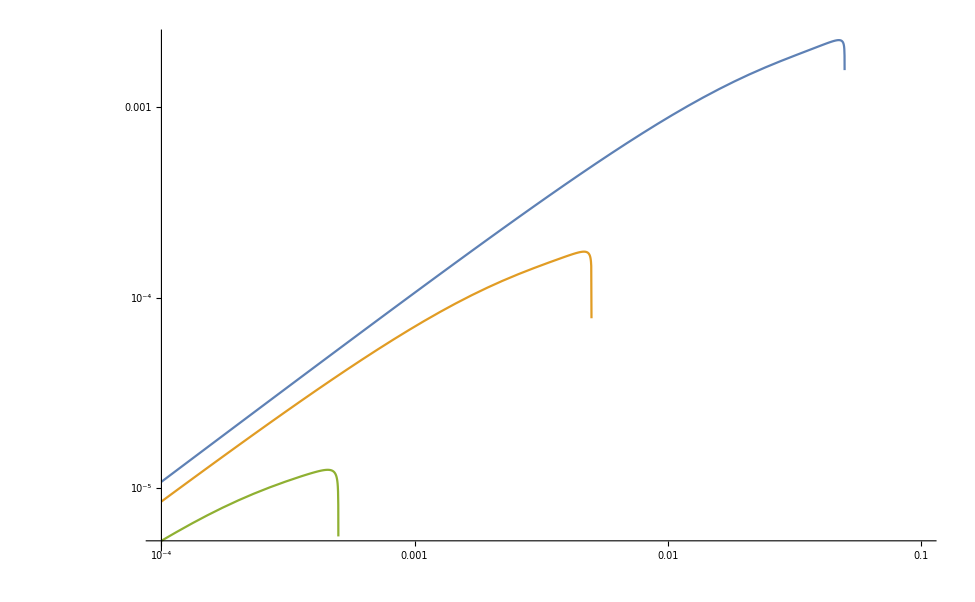

```mathematica
test=bE2dNdEeHAWC[200000./1000.,0.0011/1000.]
dNdE1e[10^((Log10[ben⟦4⟧]+Log10[ben⟦4+1⟧])/2),200000./1000.,0.0011/1000.]

tmA=0.0061 10^-3;
tmχ=200.;
tx1=0.9;
tE0=0.49 tmA;
tE1=28.0179;
(*dNdy[tx1,tmA,0.511 10^-6]
dNdx1a[tx1,(2tmA)/tmχ,(2*0.511 10^-6(*TeV*))/tmA]
dNdE1ey[tE1,tmχ,tmA]
dNdE1e[tE1,tmχ,tmA]*)
dNdE0a[tE0,tmA]
dNdE0eBr[tE0,tmA]
LogLogPlot[{E0^2 dNdE0eBr[E0,0.1],E0^2 dNdE0eBr[E0,0.01],E0^2 dNdE0eBr[E0,0.001]},{E0,10^-4,0.1}]
```

```mathematica
Γee[0.05,10^-5]
```

```mathematica
ben
10^((Log10[ben⟦3⟧]+Log10[ben⟦2⟧])/2)
```

{0.5,1.6,5.,15.7,50.,158.}

2.82843

```mathematica
Import[$perannspecfile,"TSV"]//ToExpression;
filetest=Flatten[%,1];
pointno=2;
filetest[[pointno]][[5]]
bE2dNdEeHAWC[filetest⟦pointno,1⟧/1000.,filetest⟦pointno,2⟧/1000.]
```

```mathematica
DPmasstab
```

```mathematica
(*HERE WE RUN MADGRAPH + PYTHIA FOR EACH MA', AND BIN INTO HAWC BINS*)
If[$Notebooks==False,If[FileExistsQ[$widthsfile],DeleteFile[$widthsfile]]];
If[$Notebooks==False,If[FileExistsQ[$perannspecfile],DeleteFile[$perannspecfile]]];
Do[
error="Errors: ";
If[DPmasstab⟦k⟧<0.2,
error=error<>"DP mass below 0.2";
DPw=Γee[DPmasstab⟦k⟧,MGϵ];
widthresults=OpenAppend[$widthsfile,PageWidth->500];
outlist={MGmχ,DPmasstab⟦k⟧,MGϵ,MGαχ,DPw};
If[$Notebooks==False,Write[widthresults,outlist]];
Close[widthresults];

perannspec=bE2dNdEeHAWC[DMmass/1000.,DPmasstab⟦k⟧/1000.];
specresults=OpenAppend[$perannspecfile,PageWidth->500];
outlist={MGmχ,DPmasstab⟦k⟧,MGϵ,MGαχ,perannspec,error};
If[$Notebooks==False,Write[specresults,outlist]];
Close[specresults];

];


If[DPmasstab⟦k⟧≥ 0.2&&$Notebooks==False,
ScanMadgraph[{DPmasstab⟦k⟧(*DPmtable⟦k⟧*)},1(*1  calculate wdvb Auto*)];
DPw=readwidths["50"]⟦1⟧;
If[NumberQ[DPw]==False,(DPw=$Failed;error=error<>"DPw";)];
(*If had error running Mg5 with wdvb Auto, then try running it without:*)
If[error=="Errors: "<>"DPw",ScanMadgraph[{DPmasstab⟦k⟧(*DPmtable⟦k⟧*)},0(*1  calculate wdvb Auto*)];];
widthresults=OpenAppend[$widthsfile,PageWidth->500];
outlist={MGmχ,DPmasstab⟦k⟧,MGϵ,MGαχ,DPw};
If[$Notebooks==False,Write[widthresults,outlist]];
Close[widthresults];
pythiaread[];
photonErest=Flatten[Import[$pythonoutputfile<>StringTake[fn⟦-1⟧,-2],"TSV"]];
(*If there is no numeric quantity in the photon energy list, e.g. it's failed, return fail error:*)
If[NumberQ[photonErest⟦1⟧]==False,error=error<>" Pythia"];
(*If photon energy list seems to be filled, write binned spectrum per annihilation:*)
If[NumberQ[photonErest⟦1⟧]==True,(
(*binned E^2 dN/dE per annihilation:*)
perannspec=bE2dNdE[photonErest,ben];
specresults=OpenAppend[$perannspecfile,PageWidth->500];
outlist={MGmχ,DPmasstab⟦k⟧,MGϵ,MGαχ,perannspec,error};
If[$Notebooks==False,Write[specresults,outlist]];
Close[specresults];)];
If[NumberQ[photonErest⟦1⟧]==False,(
perannspec="PythiaError";
specresults=OpenAppend[$perannspecfile,PageWidth->500];
outlist={MGmχ,DPmasstab⟦k⟧,MGϵ,MGαχ,perannspec,error};
If[$Notebooks==False,Write[specresults,outlist]];
Close[specresults];)];
];
If[error=="Errors: ",error=error<>"None"];
(*Print[error]*)
,{k,1,Length[DPmasstab]}]
```

```mathematica
(*FINDS WHAT WIDTHS DID NOT COMPUTE AND INFERS THEM FROM INTERPOLATION OF OTHER POINTS*)
widthsimp=Flatten[Import[$widthsfile,"TSV"],1]//ToExpression;
widthssel=Select[widthsimp,NumberQ[#⟦5⟧]==True&];
inttab=Table[{widthssel⟦i,2⟧,widthssel⟦i,5⟧},{i,1,Length[widthssel]}];
intfunc=Interpolation[inttab,InterpolationOrder->1];
widthsimpfix=widthsimp;
Do[
If[widthsimp⟦i,5⟧==$Failed,widthsimpfix⟦i,5⟧=intfunc[widthsimp⟦i,2⟧]];
,{i,1,Length[widthsimp]}]
Export[$widthsfixfile,widthsimpfix,"TSV"];
```

```mathematica
(*COMBINES INTO EFLUX DATA: (mχ,mA,ϵ,αχ,Γdecay,Γann,{E, E^2 dN/dE [TeV/cm^2]})*)
wfiximp=Import[$widthsfixfile,"TSV"]//ToExpression;
perannspec=Flatten[Import[$perannspecfile,"TSV"],1]//ToExpression;
eflux=wfiximp;
If[$Notebooks==False,Do[ccap=Ccap[wfiximp⟦l,1⟧,wfiximp⟦l,2⟧,wfiximp⟦l,3⟧,wfiximp⟦l,4⟧];
cann=Cann[wfiximp⟦l,1⟧,wfiximp⟦l,2⟧,wfiximp⟦l,4⟧];
tau=1/√(ccap cann);
annrate=1/2 ccap Tanh[τS/tau]^2;
eflux⟦l⟧=Append[eflux⟦l⟧,annrate];
eflux⟦l⟧=Append[eflux⟦l⟧,perannspec⟦l,5⟧/.{x_,y_}->{x,eflux⟦l,-1⟧/(4π aucm^2)y}];
eflux⟦l⟧=Append[eflux⟦l⟧,tau/τS];
,{l,1,Length[wfiximp]}]];
If[$Notebooks==False,Export[$efluxfile,eflux,"TSV"]];
```

```mathematica
(*FUNCTION THAT SCALES RESULTS BY A NEW MIXING PARAMETER*)
scaleϵ[eflux_,currentϵ_,newϵ_]:=(efluxscaled=eflux;
Do[
efluxscaled⟦i,3⟧=newϵ/currentϵ eflux⟦i,3⟧;
(*Scales decay width:*)
efluxscaled⟦i,5⟧=newϵ^2/currentϵ^2 eflux⟦i,5⟧;
(*Scales annihilation rate:*)
efluxscaled⟦i,6⟧=newϵ^2/currentϵ^2 eflux⟦i,6⟧;
(*Scales energy flux:*)
efluxscaled⟦i,7⟧=eflux⟦i,7⟧/.{x_,y_}-> {x,(newϵ^2 Tanh[(newϵ τS)/(currentϵ eflux⟦i,8⟧)]^2)/(currentϵ^2 Tanh[τS/eflux⟦i,8⟧]^2)y};
efluxscaled⟦i,8⟧=currentϵ/newϵ eflux⟦i,8⟧;
,{i,1,Length[eflux]}];
efluxscaled)
eflux=Import[$efluxfile,"TSV"]//ToExpression;
efluxscan=Flatten[Table[scaleϵ[eflux,MGϵ,ϵtab⟦j⟧],{j,1,Length[ϵtab]}],1];
Do[efluxscan⟦j,7⟧=efluxscan⟦j,7⟧/.{x_,y_}->{x,Prdetect[efluxscan⟦j,1⟧,efluxscan⟦j,2⟧,efluxscan⟦j,5⟧]y}
,{j,1,Length[efluxscan]}];
Export[$scanfile,efluxscan,"TSV"];
```

Import::nffil: File not found during Import.

Part::partd: Part specification {$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,«50»}⟦1,7⟧ is longer than depth of object.

Part::partd: Part specification {$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,«50»}⟦1,1⟧ is longer than depth of object.

Part::partd: Part specification {$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,«50»}⟦1,2⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Set::partd: Part specification efluxscan⟦j,7⟧ is longer than depth of object.

General::stop: Further output of Set::partd will be suppressed during this calculation.

```mathematica
(*PLOT AGAINST CURRENT LIMITS*)
hawcbins={{0.5,1.6,2.2 10^-12},{1.6,5.0,8.8 10^-13},{5.0,15.7,2.8 10^-13},{15.7,50.,8.1 10^-14},{50.,158.,6.3 10^-14}};
efluxscan=Import[$scanfile,"TSV"]//ToExpression;
isexc[resultpoint_]:=If[resultpoint⟦7,1,2⟧>hawcbins⟦1,3⟧||resultpoint⟦7,2,2⟧>hawcbins⟦2,3⟧||resultpoint⟦7,3,2⟧>hawcbins⟦3,3⟧||resultpoint⟦7,4,2⟧>hawcbins⟦4,3⟧||resultpoint⟦7,5,2⟧>hawcbins⟦5,3⟧,1,0]
exctab=Select[efluxscan,isexc[#]==1&];
allowtab=Select[efluxscan,isexc[#]==0&];
excplot=Table[{exctab⟦i,2⟧,exctab⟦i,3⟧},{i,1,Length[exctab]}];
allowplot=Table[{allowtab⟦i,2⟧,allowtab⟦i,3⟧},{i,1,Length[allowtab]}];
oursfull=ListLogLogPlot[{excplot,allowplot},PlotStyle->{Red,Blue},PlotMarkers-> {"■","■"},PlotRange->All,Frame-> True,FrameStyle-> Black,LabelStyle-> 18,ImageSize->800, FrameLabel->{"Dark Photon Mass (GeV)","Mixing Parameter ϵ"}];
range={{Log[1.38 10.^-3],Log[0.7 10.^3]},{Log[10.^-12],Log[0.30 10.^-2]}};
ours=ListLogLogPlot[excplot,PlotStyle->{Red,Opacity[0.5]},PlotMarkers-> "■",PlotRange->All,Frame-> True,FrameStyle-> Black,LabelStyle-> 18,ImageSize->800, AspectRatio->1., FrameLabel->{"Dark Photon Mass (GeV)","Mixing Parameter ϵ"}];
DDxenon=LogLogPlot[upperϵDD[DMmass,mA,0.024/1000 DMmass,0.05],{mA,0.001,1000.},PlotStyle->{Black,Thick}];
theirs=Import["DP_massive_current_cropped.png"];
polygonbottom=0.415;
polygonright=1.0025;
fticks[min_,max_]:=Table[If[IntegerQ[i],{Log[10^i],i,{.1,0},Red},{i,i,{.05,0},Blue}],{i,Ceiling[min],Floor[max],1}];
Show[ours,DDxenon,Frame->True,PlotRange->range,Axes->False,(*FrameTicks-> {fticks,fticks,False,False},*)ImageSize->800,AspectRatio->1,Prolog->{ Texture[theirs],Polygon[{Scaled[{0,polygonbottom}],Scaled[{polygonright,polygonbottom}],Scaled[{polygonright,1}],Scaled[{0,1}]},VertexTextureCoordinates->{{0,0},{1,0},{1,1},{0,1}}]},Epilog->{Style[Text["m_χ = "<>ToString[Round[DMmass/1000.]]<>" TeV",Scaled[{0.8,0.1}]],25,Black],Style[Text["XENON1T (2018)",Scaled[{0.12,0.2}]],15,Black]}]
```

Greater::nord: Invalid comparison with 0.+6.13054×10^-22 ⅈ attempted.

Greater::nord: Invalid comparison with 0.+1.34803×10^-21 ⅈ attempted.

Greater::nord: Invalid comparison with 0.+5.95052×10^-22 ⅈ attempted.

General::stop: Further output of Greater::nord will be suppressed during this calculation.

Greater::nord: Invalid comparison with 0.+6.13054×10^-22 ⅈ attempted.

Greater::nord: Invalid comparison with 0.+1.34803×10^-21 ⅈ attempted.

Greater::nord: Invalid comparison with 0.+5.95052×10^-22 ⅈ attempted.

General::stop: Further output of Greater::nord will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {200000.} lies outside the range of data in the interpolating function. Extrapolation will be used.

-Graphics-

```mathematica
(*PLOT AGAINST FUTURE LIMITS*)
hawcbins={{0.5,1.6,2.2 10^-12},{1.6,5.0,8.8 10^-13},{5.0,15.7,2.8 10^-13},{15.7,50.,8.1 10^-14},{50.,158.,6.3 10^-14}};
efluxscan=Import[$scanfile,"TSV"]//ToExpression;
isexc[resultpoint_]:=If[resultpoint⟦7,1,2⟧>hawcbins⟦1,3⟧||resultpoint⟦7,2,2⟧>hawcbins⟦2,3⟧||resultpoint⟦7,3,2⟧>hawcbins⟦3,3⟧||resultpoint⟦7,4,2⟧>hawcbins⟦4,3⟧||resultpoint⟦7,5,2⟧>hawcbins⟦5,3⟧,1,0]
exctab=Select[efluxscan,isexc[#]==1&];
allowtab=Select[efluxscan,isexc[#]==0&];
excplot=Table[{exctab⟦i,2⟧,exctab⟦i,3⟧},{i,1,Length[exctab]}];
allowplot=Table[{allowtab⟦i,2⟧,allowtab⟦i,3⟧},{i,1,Length[allowtab]}];
oursfull=ListLogLogPlot[{excplot,allowplot},PlotStyle->{Red,Blue},PlotMarkers-> {"■","■"},PlotRange->All,Frame-> True,FrameStyle-> Black,LabelStyle-> 18,ImageSize->800, FrameLabel->{"Dark Photon Mass (GeV)","Mixing Parameter ϵ"}];
range={{Log[1.38 10.^-3],Log[0.7 10.^3]},{Log[10.^-12],Log[0.30 10.^-2]}};
ours=ListLogLogPlot[excplot,PlotStyle->{Red,Opacity[0.5]},PlotMarkers-> "■",PlotRange->All,Frame-> True,FrameStyle-> Black,LabelStyle-> 18,ImageSize->800, AspectRatio->1., FrameLabel->{"Dark Photon Mass (GeV)","Mixing Parameter ϵ"}];
DDxenon=LogLogPlot[upperϵDD[DMmass,mA,0.024/1000 DMmass,0.05],{mA,0.001,1000.},PlotStyle->{Black,Thick}];
theirs=Import["DP_massive_future.png"];
polygonbottom=0.416;
fticks[min_,max_]:=Table[If[IntegerQ[i],{Log[10^i],i,{.1,0},Red},{i,i,{.05,0},Blue}],{i,Ceiling[min],Floor[max],1}];
Show[ours,DDxenon,Frame->True,PlotRange->range,Axes->False,(*FrameTicks-> {fticks,fticks,False,False},*)ImageSize->800,AspectRatio->1,Prolog->{ Texture[theirs],Polygon[{Scaled[{0,polygonbottom}],Scaled[{1,polygonbottom}],Scaled[{1,1}],Scaled[{0,1}]},VertexTextureCoordinates->{{0,0},{1,0},{1,1},{0,1}}]},Epilog->{Style[Text["m_χ = "<>ToString[Round[DMmass/1000.]]<>" TeV",Scaled[{0.8,0.1}]],25,Black],Style[Text["XENON1T (2018)",Scaled[{0.12,0.2}]],15,Black]}]
```

Greater::nord: Invalid comparison with 0.+6.13054×10^-22 ⅈ attempted.

Greater::nord: Invalid comparison with 0.+1.34803×10^-21 ⅈ attempted.

Greater::nord: Invalid comparison with 0.+5.95052×10^-22 ⅈ attempted.

General::stop: Further output of Greater::nord will be suppressed during this calculation.

Greater::nord: Invalid comparison with 0.+6.13054×10^-22 ⅈ attempted.

Greater::nord: Invalid comparison with 0.+1.34803×10^-21 ⅈ attempted.

Greater::nord: Invalid comparison with 0.+5.95052×10^-22 ⅈ attempted.

General::stop: Further output of Greater::nord will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {200000.} lies outside the range of data in the interpolating function. Extrapolation will be used.

-Graphics-

```mathematica
AbsoluteTiming[τ[tmχ,tmA,tϵ,tαχ]]
```

{0.16822,2.87223×10^16}

```mathematica
(*PLOT WITH EQUILIBRIUM*)
hawcbins={{0.5,1.6,2.2 10^-12},{1.6,5.0,8.8 10^-13},{5.0,15.7,2.8 10^-13},{15.7,50.,8.1 10^-14},{50.,158.,6.3 10^-14}};
ϵstart=10^-5.;
mAscan=Table[{10^lmA,ϵstart,τ[DMmass,10^lmA,ϵstart,0.024/1000. DMmass]/τS},{lmA,-3.,3.,6/100.}];
ϵscan=Table[{mAscan⟦i,1⟧,10^lϵ,ϵstart/10^lϵ mAscan⟦i,3⟧},{i,1,Length[mAscan]},{lϵ,-12.,-4.,8/100.}];
ϵscan=Flatten[ϵscan,1];
ϵscan=Select[ϵscan,NumberQ[#⟦3⟧]==True&];
```

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

```mathematica
efluxscan=Import[$scanfile,"TSV"]//ToExpression
isexc[resultpoint_]:=If[resultpoint⟦7,1,2⟧>hawcbins⟦1,3⟧||resultpoint⟦7,2,2⟧>hawcbins⟦2,3⟧||resultpoint⟦7,3,2⟧>hawcbins⟦3,3⟧||resultpoint⟦7,4,2⟧>hawcbins⟦4,3⟧||resultpoint⟦7,5,2⟧>hawcbins⟦5,3⟧,1,0]
exctab=Select[efluxscan,isexc[#]==1&];
allowtab=Select[efluxscan,isexc[#]==0&];
(*notequiltab=Select[efluxscan,#⟦8⟧>1&];*)
notequiltab=Select[ϵscan,#⟦3⟧>1&];
excplot=Table[{exctab⟦i,2⟧,exctab⟦i,3⟧},{i,1,Length[exctab]}];
allowplot=Table[{allowtab⟦i,2⟧,allowtab⟦i,3⟧},{i,1,Length[allowtab]}];
(*notequilplot=Table[{notequiltab⟦i,2⟧,notequiltab⟦i,3⟧},{i,1,Length[notequiltab]}];*)
notequilplot=Table[{notequiltab⟦i,1⟧,notequiltab⟦i,2⟧},{i,1,Length[notequiltab]}];
oursfull=ListLogLogPlot[{excplot,allowplot},PlotStyle->{Red,Blue},PlotMarkers-> {"■","■"},PlotRange->All,Frame-> True,FrameStyle-> Black,LabelStyle-> 18,ImageSize->800, FrameLabel->{"Dark Photon Mass (GeV)","Mixing Parameter ϵ"}];
range={{Log[1.38 10.^-3],Log[0.7 10.^3]},{Log[10.^-12],Log[0.30 10.^-2]}};
ours=ListLogLogPlot[excplot,PlotStyle->{Red,Opacity[0.5]},PlotMarkers-> "■",PlotRange->All,Frame-> True,FrameStyle-> Black,LabelStyle-> 18,ImageSize->800, AspectRatio->1., FrameLabel->{"Dark Photon Mass (GeV)","Mixing Parameter ϵ"}];
equil=ListLogLogPlot[notequilplot,PlotStyle->{Orange,Opacity[0.5]},PlotMarkers-> "■",PlotRange->All,Frame-> True,FrameStyle-> Black,LabelStyle-> 18,ImageSize->800, AspectRatio->1., FrameLabel->{"Dark Photon Mass (GeV)","Mixing Parameter ϵ"}];
DDxenon=LogLogPlot[upperϵDD[DMmass,mA,0.024/1000 DMmass,0.05],{mA,0.001,1000.},PlotStyle->{Black,Thick}];
theirs=Import["DP_massive_future.png"];
polygonbottom=0.416;
fticks[min_,max_]:=Table[If[IntegerQ[i],{Log[10^i],i,{.1,0},Red},{i,i,{.05,0},Blue}],{i,Ceiling[min],Floor[max],1}];
Show[ours,equil,DDxenon,Frame->True,PlotRange->range,Axes->False,(*FrameTicks-> {fticks,fticks,False,False},*)ImageSize->800,AspectRatio->1,Prolog->{ Texture[theirs],Polygon[{Scaled[{0,polygonbottom}],Scaled[{1,polygonbottom}],Scaled[{1,1}],Scaled[{0,1}]},VertexTextureCoordinates->{{0,0},{1,0},{1,1},{0,1}}]},Epilog->{Style[Text["m_χ = "<>ToString[Round[DMmass/1000.]]<>" TeV",Scaled[{0.8,0.1}]],25,Black],Style[Text["XENON1T (2018)",Scaled[{0.12,0.2}]],15,Black]}]
```

{{200000.,0.001,1.×10^-10,4.8,0.+7.81167×10^-27 ⅈ,3.49002×10^17,{{0.894427,0.+6.13054×10^-22 ⅈ},{2.82843,0.+1.34803×10^-21 ⅈ},{8.86002,0.+5.95052×10^-22 ⅈ},{28.0179,0.-1.45276×10^-20 ⅈ},{88.8819,0.-7.13016×10^-21 ⅈ}},6.17685×10^-6},9998,{200000.,10.,0.01,4.8,0.0000169114,2.38358×10^20,{{0.894427,0.},{2.82843,0.},{8.86002,0.},{28.0179,0.},{88.8819,0.}},7.81255×10^-7}}
 |  |  |  |

Greater::nord: Invalid comparison with 0.+6.13054×10^-22 ⅈ attempted.

Greater::nord: Invalid comparison with 0.+1.34803×10^-21 ⅈ attempted.

Greater::nord: Invalid comparison with 0.+5.95052×10^-22 ⅈ attempted.

General::stop: Further output of Greater::nord will be suppressed during this calculation.

Greater::nord: Invalid comparison with 0.+6.13054×10^-22 ⅈ attempted.

Greater::nord: Invalid comparison with 0.+1.34803×10^-21 ⅈ attempted.

Greater::nord: Invalid comparison with 0.+5.95052×10^-22 ⅈ attempted.

General::stop: Further output of Greater::nord will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {200000.} lies outside the range of data in the interpolating function. Extrapolation will be used.

-Graphics-

```mathematica
DPmasstab
```

```mathematica
testgraph=stylelist⟦50⟧//InputForm;
testgraph
```

```mathematica
Show[ours,testgraph,Frame->True,Axes->False,ImageSize->800,AspectRatio->1,PlotRange->All]
```

```mathematica
theirs=Import["DP_massive_future.pdf"]//InputForm;
spos=Position[theirs,Style];
stylelist=Table[Extract[theirs,Most@spos⟦n⟧],{n,1,Length[spos]}];
styletographicslist=Table[Graphics[stylelist⟦n⟧],{n,1,Length[spos]}];

Manipulate[styletographicslist⟦n⟧,{n,1,Length[pos],1}]
```

```mathematica
testgraph=stylelist⟦50⟧
Show[Graphics[testgraph],PlotRange->Full,Frame->True,Prolog->{testgraph}]
```

## Plotting

```mathematica
(*PLOTTING WIDTH*)
widthsimp=Flatten[Import[$widthsfile,"TSV"],1]//ToExpression
plottab=Table[{widthsimp⟦i,2⟧,widthsimp⟦i,5⟧},{i,1,Length[widthsimp]}];
(*Removes ones with failed widths:*)
Select[plottab,NumberQ[#⟦2⟧]==True&];
plottab⟦1,2⟧;
ListPlot[plottab,Frame->True,FrameLabel->{"Dark Photon Mass (GeV)","Decay Width (GeV)"},FrameStyle->Black,LabelStyle->25,ImageSize->800,Epilog->{Style[Text["ϵ = "<>ToString[ScientificForm[MGϵ,NumberFormat->(#1<>"E"<>#3&)]],Scaled[{0.7,0.3}]],20,Black],Style[Text["m_χ = "<>ToString[Round[DMmass/1000.]]<>" TeV",Scaled[{0.7,0.2}]],20,Black]}]
```

```mathematica
(*PLOTTING RAW SPECTRUM OUT OF PYTHIA AGAINST BOOSTED ANALYTICAL SPECTRUM*)
dNdx0a[x0_,ϵf_]:=(1/137.)/π(1+(1-x0)^2)/x0(Log[(4(1-x0))/ϵf^2]-1);
(*Boosting the spectrum:*)
dNdx1a[x1_,ϵ1_,ϵf_]:=(t1maxa=Min[1,(2x1)/ϵ1^2(1+√(1-ϵ1^2))];
t1mina=(2x1)/ϵ1^2(1-√(1-ϵ1^2));
2NIntegrate[1/(x0 √(1-ϵ1^2))dNdx0a[x0,ϵf],{x0,t1mina,t1maxa}])(*boosted photon spectrum for two mediators*);
dNdE1e[En_,mχ_,mA_]:=1/mχ dNdx1a[En/mχ,(2mA)/mχ,(2*0.511 10^-6(*TeV*))/mA];
(*SPECTRUM BEFORE ANY BOOST*)
runnumber=1;
photonErest=Flatten[Import[$pythonoutputfile<>StringTake[fn⟦runnumber⟧,-2],"TSV"]];
DPmass=DPmasstab⟦runnumber⟧
DMmassTeV=DMmass/1000.;
DPmassTeV=DPmass/1000.;
minbin=0.5 (*10^-5 DMmassTeV*)
maxbin=158.(*DMmassTeV*)
Log10[maxbin]
Log10[minbin]
nobins=5;
(Log10[minbin]-Log10[maxbin])/nobins
bins=Table[10^le,{le,Log10[minbin],Log10[maxbin],(Log10[maxbin]-Log10[minbin])/nobins}]

(*binned photon energies*)
bpe[spectrum_,bins_]:=(binnedE={};
Do[bin=Select[spectrum,bins⟦i⟧<#<bins⟦i+1⟧&];
binnedE=Append[binnedE,bin];
,{i,1,Length[bins]-1}];
binnedE)
(*Binned dN/dE from energies list. Returns list of {dNdE, Energy} in TeV*)
bdNdE[spectrum_,bins_]:=(binnedpe=bpe[spectrum,bins];
dNdElist={};
Do[
dN=Length[binnedpe⟦i⟧];
dE=bins⟦i+1⟧-bins⟦i⟧;
dNdEpoint={(bins⟦i+1⟧+bins⟦i⟧)/2,1/((*per annihilation*)nevents)dN/dE};
dNdElist=Append[dNdElist,dNdEpoint];
,{i,1,Length[binnedpe]}];
dNdElist
)
(*Binned E^2 dN/dE*)
bE2dNdE[spectrum_,bins_]:=(binnedpe=bpe[spectrum,bins];
dNdElist={};
Do[
dN=Length[binnedpe⟦i⟧];
dE=bins⟦i+1⟧-bins⟦i⟧;
dNdEpoint={(bins⟦i+1⟧+bins⟦i⟧)/2,((bins⟦i+1⟧+bins⟦i⟧)/2)^2 1/nevents dN/dE};
dNdElist=Append[dNdElist,dNdEpoint];
,{i,1,Length[binnedpe]}];
dNdElist
)

(*Show[LogLogPlot[dNdE0a[en,DPmassTeV],{en,minbin,maxbin}],ListLogLogPlot[bdNdE[photonErest,bins],PlotStyle->Green],Frame->True,FrameLabel->{"Photon Energy (TeV)","dN/dE (TeV^-1)"},FrameStyle->Black,LabelStyle->25,ImageSize->800,Epilog->{Style[Text["m_A' = "<>ToString[DPmass]<>" GeV",Scaled[{0.5,0.2}]],20,Black]}]
*)
bE2dNdEeHAWC[mχ_,mA_]:=Table[{10^((Log10[ben⟦i⟧]+Log10[ben⟦i+1⟧])/2),(10^((Log10[ben⟦i⟧]+Log10[ben⟦i+1⟧])/2))^2 dNdE1e[10^((Log10[ben⟦i⟧]+Log10[ben⟦i+1⟧])/2),mχ,mA]},{i,1,Length[ben]-1}]

Show[LogLogPlot[en^2 dNdE1e[en,DMmassTeV,DPmassTeV],{en,minbin,maxbin}],ListLogLogPlot[bE2dNdE[photonErest,bins],PlotStyle->Green],ListLogLogPlot[bE2dNdEeHAWC[DMmassTeV,DPmassTeV],PlotStyle->Red],Frame->True,FrameLabel->{"Photon Energy (TeV)","E^2dN/dE (TeV)"},FrameStyle->Black,LabelStyle->25,ImageSize->800,Epilog->{Style[Text["m_A' = "<>ToString[DPmass]<>" GeV",Scaled[{0.7,0.3}]],20,Black],Style[Text["m_χ = "<>ToString[Round[DMmassTeV]]<>" TeV",Scaled[{0.7,0.2}]],20,Black]},PlotRange->All]
```

```mathematica
dNdElist
bE2dNdEeHAWC[DMmassTeV,DPmassTeV]
```

```mathematica
{{0.894427190999916,0.18281454545454545},{2.8284271247461903,0.5163141176470588},{8.860022573334678,1.2414196261682244},{28.017851452243807,2.7748864285714294},{88.88194417315589,1.8026666666666666}}
```

```mathematica
(*ANALYTICAL SPECTRUM FOR ELECTRONS NOT TRUNCATED*)
dNdx0a[x0_,ϵf_]:=(1/137.)/π(1+(1-x0)^2)/x0(Log[(4(1-x0))/ϵf^2]-1);
(*Boosting the spectrum:*)
dNdx1a[x1_,ϵ1_,ϵf_]:=(t1maxa=Min[1,(2x1)/ϵ1^2(1+√(1-ϵ1^2))];
t1mina=(2x1)/ϵ1^2(1-√(1-ϵ1^2));
2NIntegrate[1/(x0 √(1-ϵ1^2))dNdx0a[x0,ϵf],{x0,t1mina,t1maxa}])(*boosted photon spectrum for two mediators*);
dNdE1e[En_,mχ_,mA_]:=1/mχ dNdx1a[En/mχ,(2mA)/mχ,(2*0.511 10^-6(*TeV*))/mA];
LogLogPlot[{en^2 dNdE1e[en,100.,10.^-3],en^2 dNdE1e[en,100.,10.^-5],en^2 dNdE1e[en,100.,5 10.^-6],en^2 dNdE1e[en,100.,1.1 10.^-6]},{en,0.0001,100.}]
```

```mathematica
SetDirectory[NotebookDirectory[]];
Import["DP_massive_future.pdf","PDF"]
```

```mathematica
Import["DP_massive_future_cropped.pdf"]
```

```mathematica
xenontabfull=Import["data/xenonDD.csv"]
xenonint=Interpolation[xenontabfull,InterpolationOrder->1];
```

```mathematica
Export["data/xenonDD.csv",xenontabfull]
```

```mathematica
Import["data/xenonDD.csv"]
```